## Fig. S8A

Generate species richness plots for lattice territory model with many random communities.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];

Needs["ErrorBarLogPlots`"];
```

### get color scheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### iteratively load data and analyze

```mathematica
getRichness[n_]:=Block[{},
nTotal=Total[n];
cutoff=10^-6;
richness=Count[n,x_/;x>cutoff]
]
```

```mathematica
geometrySet={"linear","square","hexagonal","linear_noOligo","square_noOligo","hexagonal_noOligo"};
```

```mathematica
sMeans=ConstantArray[0,Length[geometrySet]];
sStds=ConstantArray[0,Length[geometrySet]];
```

```mathematica
For[i=1,i≤6,i++,
allFP=Import["data\\lDiversity_s1pt4_"<>geometrySet[[i]]<>"_allFP.mx"];

lengths=Length/@allFP;
validFPIndices=Position[lengths,x_/;x==9];

validFP=allFP[[validFPIndices//Flatten]];

(*-2 corresponds to tau=1*)
theseS=Table[getRichness[validFP[[i,-2]]]/16,{i,Length[validFP]}];

sMeans[[i]]=Mean[theseS];
sStds[[i]]=StandardDeviation[theseS];

]
```

### plotting

```mathematica
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]
```

```mathematica
chartData=Table[sMeans[[i]]->sStds[[i]],{i,Length[sMeans]}];
```

```mathematica
labelSet={"1D","Square","Hexagonal"};
```

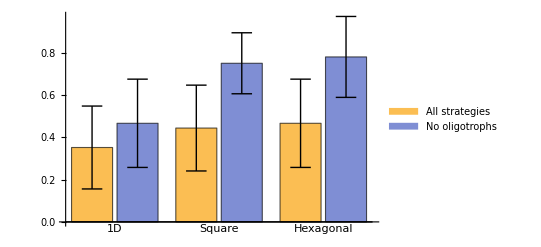

```mathematica
BarChart[{{chartData[[1]],chartData[[3]]},{chartData[[2]],chartData[[4]]},{chartData[[3]],chartData[[6]]}},ChartElementFunction->errorBar["Rectangle"], ChartLabels->{Placed[labelSet,Automatic],Placed[{"",""},Center]},TicksStyle->Directive[Black, 12],(*Ticks->{Automatic,Range[0.0,1.0,0.2]},*)LabelStyle->Directive[Black,FontSize->14,FontFamily->"Helvetica"],ChartLegends->{"All strategies","No oligotrophs"}]
```

```mathematica
Export["figS8A_speciesRichness.svg",%];
```